```mathematica
ClearAll["Global`*"]
```

```mathematica
α[R_, Ω_] := 1/(√2)(1+ ⅈ)√(R Ω);
u[y_,t_, R_, Ω_] := Re[1/(R Ω ⅈ) (1-Cosh[α[R,Ω] y]/Cosh[α[R,Ω]])ⅇ^(ⅈ Ω t)]
```

```mathematica
XXX[y_, R_, Ω_] :=1/(R Ω)(Cosh[Re[α[R, Ω]]y]Sinh[Re[α[R, Ω]]]Cos[Im[α[R, Ω]]y]Sin[Im[α[R, Ω]]]
- Cosh[Re[α[R, Ω]]]Sinh[Re[α[R, Ω]]y]Cos[Im[α[R, Ω]]]Sin[Im[α[R, Ω]]y]) (Cosh[Re[α[R,Ω]]]^2 Cos[Im[α[R, Ω]]]^2 + Sinh[Re[α[R, Ω]]]^2 Sin[Im[α[R, Ω]]]^2)^-1
```

```mathematica
Manipulate[Plot[u[y, t, 100,0.1], {y,-1,1}], {t,0,100,0.5}]
```

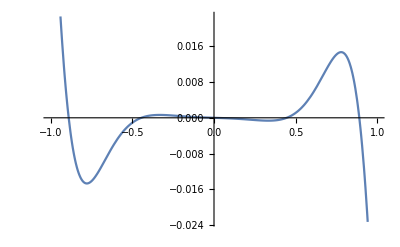

```mathematica
Plot[{D[XXX[ys, 100, 1], ys]/.ys->y}, {y,-1,1}]
```

```mathematica
NSolve[D[XXX[ys, 100, 1], ys]==0/.ys->y, {y}]
```

{y→-0.888928}

```mathematica
ClearAll["Global`*"]
```

```mathematica
α[R_,Wi_,β_, Ω_] := 1/(√2)(1+ ⅈ)√(R Ω*(1.0+Wi Ω ⅈ)/(1.0+Wi Ω β ⅈ));
u[y_, R_,Wi_,β_, Ω_] = Re[1/(R Ω ⅈ) (1-Cosh[α[R,Wi,β, Ω] y]/Cosh[α[R,Wi,β, Ω]])];
dudy[y_,R_,Wi_,β_, Ω_]=α[R,Wi,β, Ω]/(R Ω ⅈ) (Sinh[α[R,Wi,β, Ω] y]/Cosh[α[R,Wi,β, Ω]]);
cxx[y_,R_,Wi_,β_, Ω_]= Re[(2 Wi^2)/(1+ Wi ⅈ Ω)^2(dudy[y,R,Wi,β, Ω])^2+1];
cxy[y_,R_,Wi_,β_, Ω_]= Re[Wi/(1+ Wi ⅈ Ω)(dudy[y,R,Wi,β, Ω])];
```

```mathematica
R = 1;
Wi = 1.0;
β = 0.01;
Ω = 10;
```

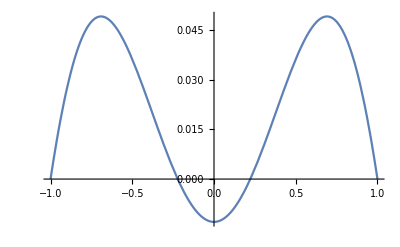

```mathematica
Plot[u[y,R,Wi,β,Ω], {y,-1,1}]
```

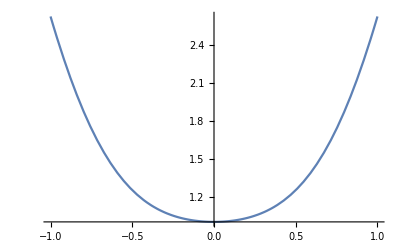

```mathematica
Plot[cxx[y,R,Wi,β,Ω], {y,-1,1}]
```

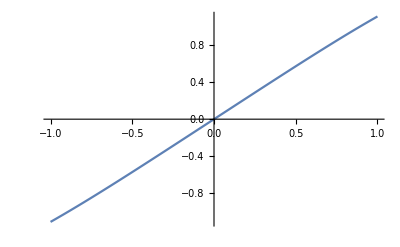

```mathematica
Plot[cxy[y,R,Wi,β,Ω], {y,-1,1}]
```

```mathematica
FullSimplify[((1-Cosh[((1+ⅈ) y √((R Ω (1.+ⅈ Wi Ω))/(1.+ⅈ Wi β Ω)))/(√2)] Sech[((1+ⅈ) √((R Ω (1.+ⅈ Wi Ω))/(1.+ⅈ Wi β Ω)))/(√2)])/(R Ω)-Conjugate[(1-Cosh[((1+ⅈ) y √((R Ω (1.+ⅈ Wi Ω))/(1.+ⅈ Wi β Ω)))/(√2)] Sech[((1+ⅈ) √((R Ω (1.+ⅈ Wi Ω))/(1.+ⅈ Wi β Ω)))/(√2)])/(R Ω)])/2, y∈Reals]
```

(-0.0188627-0.00441241 ⅈ) Cos[(3.3899+1.6064 ⅈ) y]+(0.0188627-0.00441241 ⅈ) Cosh[(1.6064+3.3899 ⅈ) y]

```mathematica
Ke = NIntegrate[u[y,R,Wi,β,Ω], {y,-1,1}]
```

1.27177